# get n, v, then do 1/nv

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
nbar[ωtr_,T_]:=1/(Exp[ℏ ωtr/kB/T]-1);
Δnbar[ωtr_,T_,Δωtr_,ΔT_]:=√((D[nbar[ωtr0,T], ωtr0]Δωtr)^2+ (D[nbar[ωtr,T0], T0]ΔT)^2)/.{T0->T,ωtr0->ωtr};
```

```mathematica
ωtrNa=2π 80kHz;
ωtrCs=2π 80kHz;

TNa=16.4uK;70uK/2;
TCs=10uK;

ΔωtrNa=0.1ωtrNa;
ΔTNa=0.1TNa;

ΔωtrCs=0.1ωtrCs;
ΔTCs=0.1TCs;

nbarNa=nbar[ωtrNa,TNa];
ΔnbarNa=Δnbar[ωtrNa,TNa,ΔωtrNa,ΔTNa];

nbarCs=nbar[ωtrCs,TCs];
ΔnbarCs=Δnbar[ωtrCs,TCs,ΔωtrCs,ΔTCs];
```

```mathematica
(*Na: 0.4--> 500kHz/sqrt(4) 500/6/2, pm 10%
Cs: (at raman cooling depth)
70uK for Na before lowering from .4 to .1. goes with trapping frequency. so 70uK/sqt(4)=35uK
*)
```

```mathematica
Pn[n_,nbar_]:=nbar^n/(1+nbar)^(n+1);

maxCs=10nbarCs;10;5;
maxNa=10nbarNa;15;10;


(*avg rel velocity*)
VarP[m_,nbar_,ωtr_,max_]:=Sum[ Pn[n,nbar](m ℏ ωtr)/2(2n+1),{n,0,max}];
ΔVarP[m_,nbar_,ωtr_,max_,Δnbar_,Δωtr_]:=√((D[VarP[m,nbar0,ωtr,max], nbar0]Δnbar)^2+(D[VarP[m,nbar,ωtr0,max], ωtr0]Δωtr)^2)/.{ωtr0->ωtr,nbar0->nbar};

VarPNa=VarP[mNa,nbarNa,ωtrNa,maxNa];
ΔVarPNa=ΔVarP[mNa,nbarNa,ωtrNa,maxNa,ΔnbarNa,ΔωtrNa];

VarPCs=VarP[mCs,nbarCs,ωtrCs,maxCs];
ΔVarPCs=ΔVarP[mCs,nbarCs,ωtrCs,maxCs,ΔnbarCs,ΔωtrCs];

vRel[VarPNa_,VarPCs_]:=Sqrt[3]Sqrt[VarPNa/mNa^2+VarPCs/mCs^2];
ΔvRel[VarPNa_,VarPCs_,ΔVarPNa_,ΔVarPCs_]:=√((D[vRel[VarPNa0,VarPCs], VarPNa0]ΔVarPNa)^2+(D[vRel[VarPNa,VarPCs0], VarPCs0]ΔVarPCs)^2)/.{VarPCs0->VarPCs,VarPNa0->VarPNa};

(*avg rel distance*)

VarX[m_,nbar_,ωtr_,max_]:=Sum[ Pn[n,nbar] ℏ/(2 m ωtr)(2n+1),{n,0,max}];
ΔVarX[m_,nbar_,ωtr_,max_,Δnbar_,Δωtr_]:=√((D[VarX[m,nbar0,ωtr,max], nbar0]Δnbar)^2+(D[VarX[m,nbar,ωtr0,max], ωtr0]Δωtr)^2)/.{ωtr0->ωtr,nbar0->nbar};

VarXNa=VarX[mNa,nbarNa,ωtrNa,maxNa];
ΔVarXNa=ΔVarX[mNa,nbarNa,ωtrNa,maxNa,ΔnbarNa,ΔωtrNa];

VarXCs=VarX[mCs,nbarCs,ωtrCs,maxCs];
ΔVarXCs=ΔVarX[mCs,nbarCs,ωtrCs,maxCs,ΔnbarCs,ΔωtrCs];

n[VarXNa_,VarXCs_]:=1/(Sqrt[VarXNa+VarXCs])^3;
Δn[VarXNa_,VarXCs_,ΔVarXNa_,ΔVarXCs_]:=√((D[n[VarXNa0,VarXCs], VarXNa0]ΔVarXNa)^2+(D[n[VarXNa,VarXCs0], VarXCs0]ΔVarXCs)^2)/.{VarXCs0->VarXCs,VarXNa0->VarXNa};

vvRel=vRel[VarPNa,VarPCs];
ΔvvRel=ΔvRel[VarPNa,VarPCs,ΔVarPNa,ΔVarPCs];

nn=n[VarXNa,VarXCs];
Δnn=Δn[VarXNa,VarXCs,ΔVarXNa,ΔVarXCs];
nn/cm^-3
Δnn/cm^-3
```

2.37965×10^14

5.54504×10^13

```mathematica
τLoss=80ms;36ms;
ΔτLoss=8ms;5ms;
σ[n_,τLoss_,vRel_]:=1/(n τLoss vRel);
Δσ[n_,τLoss_,vRel_,Δn_,ΔτLoss_,ΔvRel_]:=√((D[σ[n0,τLoss,vRel], n0]Δn)^2+(D[σ[n,τLoss0,vRel], τLoss0]ΔτLoss)^2+(D[σ[n,τLoss,vRel0], vRel0]ΔvRel)^2)/.{n0->n,τLoss0->τLoss,vRel0->vRel};
Print["cross section in cm^2, error bar"]
σ[nn,τLoss,vvRel]/(cm^2)
Δσ[nn,τLoss,vvRel,Δnn,ΔτLoss,ΔvvRel]/(cm^2)
```

cross section in cm^2, error bar

3.73885×10^-15

9.91541×10^-16

```mathematica
vvRel/(nm/us)
```

140.495

# get 1/nv, then do thermal average. isotropic trap

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
nbar[ωtr_,T_]:=1./(Exp[ℏ ωtr/kB/T]-1);
Δnbar[ωtr_,T_,Δωtr_,ΔT_]:=√((D[nbar[ωtr0,T], ωtr0]Δωtr)^2+ (D[nbar[ωtr,T0], T0]ΔT)^2)/.{T0->T,ωtr0->ωtr};
```

```mathematica
(****************************)
ωtrNa=2π (131.837 123.048 24.1701 )^(1/3)kHz;
 (*{Ttrap,frad1,frad2,fax}={.311mK,131.837 kHz,123.048 kHz,24.1701 kHz};*)
ωtrCs=2π (150 140 27.5)^(1/3)kHz;
(*{fxCs,fyCs,fzCs}={150,140,27.5}*)

ΔωtrNa=0.1ωtrNa;
ΔωtrCs=0.1ωtrCs;

TNa=42uK;16.4uK;70uK/2;
ΔTNa=1uK;

TCs=90uK;.01uK;110uK;
ΔTCs=0.1TCs;
(******************************)
```

```mathematica
Pn[n_,nbar_]:=1. nbar^n/(1+nbar)^(n+1);

maxCs=6Ceiling[nbar[ωtrCs,TCs]];10;5;
maxNa=6Ceiling[nbar[ωtrNa,TNa]];15;10;


(*avg rel velocity*)
VarP[n_,m_,ωtr_]:=1.(m ℏ ωtr)/2(2n+1);
VarX[n_,m_,ωtr_]:=1. ℏ/(2 m ωtr)(2n+1);

τLoss=7ms;36ms;
ΔτLoss=1ms;5ms;
Clear[σ,Δσ]

σ[TCs_,TNa_,τLoss_,ωtrNa_,ωtrCs_,maxNa_,maxCs_]:=1. Accumulate[Flatten[Table[
Pn[nCs,nbar[ωtrCs,TCs]]Pn[nNa,nbar[ωtrNa,TNa]]

1./(τLoss Sqrt[3]Sqrt[VarP[nNa,mNa,ωtrNa]/mNa^2+VarP[nCs,mCs,ωtrCs]/mCs^2]/(Sqrt[VarX[nNa,mNa,ωtrNa]+VarX[nCs,mCs,ωtrCs]])^3)
,
{nNa,0,maxNa},
{nCs,0,maxCs}]]][[-1]];

(*not quite because nbar and ωtr are correlated....*)
Δσ[TCs_,TNa_,τLoss_,ωtrNa_,ωtrCs_,maxNa_,maxCs_,ΔTCs_,ΔTNa_,ΔτLoss_,ΔωtrNa_,ΔωtrCs_]:=
Sqrt[
(D[σ[TCs0,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs], TCs0])^2 ΔTCs^2+
(D[σ[TCs,TNa0,τLoss,ωtrNa,ωtrCs,maxNa,maxCs], TNa0])^2 ΔTNa^2+
(D[σ[TCs,TNa,τLoss0,ωtrNa,ωtrCs,maxNa,maxCs], τLoss0])^2 ΔτLoss^2+
(D[σ[TCs,TNa,τLoss,ωtrNa0,ωtrCs,maxNa,maxCs], ωtrNa0])^2 ΔωtrNa^2+
(D[σ[TCs,TNa,τLoss,ωtrNa,ωtrCs0,maxNa,maxCs], ωtrCs0])^2 ΔωtrCs^2
]/.{TCs0->TCs,TNa0->TNa,τLoss0->τLoss,ωtrNa0->ωtrNa,ωtrCs0->ωtrCs};

β[TCs_,TNa_,τLoss_,ωtrNa_,ωtrCs_,maxNa_,maxCs_]:=1. Accumulate[Flatten[Table[
Pn[nCs,nbar[ωtrCs,TCs]]Pn[nNa,nbar[ωtrNa,TNa]]

1.(Sqrt[VarX[nNa,mNa,ωtrNa]+VarX[nCs,mCs,ωtrCs]])^3/(τLoss)
,
{nNa,0,maxNa},
{nCs,0,maxCs}]]][[-1]];
```

```mathematica
σ[TCs,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs]/cm^2
β[TCs,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs]/cm^3

(*Δσ[TCs,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs,ΔTCs,ΔTNa,ΔτLoss,ΔωtrNa,ΔωtrCs]/cm^2*)
```

1.57898×10^-13

4.74105×10^-12

```mathematica
1/τnv=sigma
```

```mathematica
Sqrt[VarX[0,mNa,ωtrNa]+VarX[0,mCs,ωtrCs]]/nm
```

58.8109

# get 1/nv, then do thermal average. anisotropic trap put in an isotropic trap by hand, make sure you get same answer as isotropic case.... check correspondence b/t isotropic and anisotropic for low temperature case first. --pretty close!! can also write explicit for loop and check ouptut at each step.

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
nbar[ωtr_,T_]:=1./(Exp[ℏ ωtr/kB/T]-1);
Δnbar[ωtr_,T_,Δωtr_,ΔT_]:=√((D[nbar[ωtr0,T], ωtr0]Δωtr)^2+ (D[nbar[ωtr,T0], T0]ΔT)^2)/.{T0->T,ωtr0->ωtr};
```

```mathematica
ωtrNa=2π {131.837,123.048,24.1701 }kHz;2π 80kHz; 
 (*{Ttrap,frad1,frad2,fax}={.311mK,131.837 kHz,123.048 kHz,24.1701 kHz};*)
ωtrCs=2π {150,140,27.5}kHz;
(*{fxCs,fyCs,fzCs}={150,140,27.5}*)

ωtrNa=(ωtrNa[[1]] ωtrNa[[2]] ωtrNa[[3]])^(1/3){1,1,1}; 
ωtrCs=(ωtrCs[[1]] ωtrCs[[2]] ωtrCs[[3]])^(1/3){1,1,1}; 

TNa=1uK;16.4uK;42uK;16.4uK;70uK/2;
ΔTNa=.1TNa;1.5uK;

TCs=1uK;20uK;110uK;
ΔTCs=0.1TCs;

ΔωtrNa=0.1ωtrNa;

ΔωtrCs=0.1ωtrCs;



(**********************************)
ωtrNa=2π {131.837,123.048,24.1701 }kHz;2π 80kHz; 
 (*{Ttrap,frad1,frad2,fax}={.311mK,131.837 kHz,123.048 kHz,24.1701 kHz};*)
ωtrCs=2π {150,140,27.5}kHz;
(*{fxCs,fyCs,fzCs}={150,140,27.5}*)

TNa=1uK;42uK;16.4uK;70uK/2;
ΔTNa=1.5uK;

TCs=1uK;20uK;110uK;
ΔTCs=0.1TCs;
(*************************************)
maxCs=3Ceiling[nbar[ωtrCs,TCs]]; (*ideally, 6 Ceiling nbar*)
maxNa=3Ceiling[nbar[ωtrNa,TNa]];
```

```mathematica
Pn[n_,nbar_]:=1. nbar^n/(1+nbar)^(n+1);


(*avg rel velocity*)
VarP[n_,m_,ωtr_]:=1.(m ℏ ωtr)/2(2n+1);
VarX[n_,m_,ωtr_]:=1. ℏ/(2 m ωtr)(2n+1);

τLoss=15ms;36ms;
ΔτLoss=5ms;5ms;
```

```mathematica
σ[TCs_,TNa_,τLoss_,ωtrNa1_,ωtrNa2_,ωtrNa3_,ωtrCs1_,ωtrCs2_,ωtrCs3_,maxNa1_,maxNa2_,maxNa3_,maxCs1_,maxCs2_,maxCs3_]:=


(*loosest axis goes LAST.Last sum will be innermost sum (ie, looped over the most times) 
loosest axis has highest nbar, therefore highest number of n's contributing. 
*)
Accumulate[Flatten[Table[
1. Pn[nCs1,nbar[ωtrCs1,TCs]]Pn[nNa1,nbar[ωtrNa1,TNa]] Pn[nCs2,nbar[ωtrCs2,TCs]]Pn[nNa2,nbar[ωtrNa2,TNa]] Pn[nCs3,nbar[ωtrCs3,TCs]]Pn[nNa3,nbar[ωtrNa3,TNa]]/(τLoss Sqrt[
VarP[nNa1,mNa,ωtrNa1]/mNa^2+VarP[nCs1,mCs,ωtrCs1]/mCs^2+VarP[nNa2,mNa,ωtrNa2]/mNa^2+VarP[nCs2,mCs,ωtrCs2]/mCs^2 +VarP[nNa3,mNa,ωtrNa3]/mNa^2+VarP[nCs3,mCs,ωtrCs3]/mCs^2]/(Sqrt[
(VarX[nNa1,mNa,ωtrNa1]+VarX[nCs1,mCs,ωtrCs1]) (VarX[nNa2,mNa,ωtrNa2]+VarX[nCs2,mCs,ωtrCs2]) (VarX[nNa3,mNa,ωtrNa3]+VarX[nCs3,mCs,ωtrCs3])
]))
,
{nNa1,0,maxNa1},
{nCs1,0,maxCs1},
{nNa2,0,maxNa2},
{nCs2,0,maxCs2},
{nNa3,0,maxNa3},
{nCs3,0,maxCs3}]]] ;(*[[-1]]*)
```

```mathematica
σ[TCs,TNa,τLoss,ωtrNa[[1]],ωtrNa[[2]],ωtrNa[[3]],ωtrCs[[1]],ωtrCs[[2]],ωtrCs[[3]],maxNa[[1]],maxNa[[2]],maxNa[[3]],maxCs[[1]],maxCs[[2]],maxCs[[3]]]/cm^2
```

{1.25925×10^-15,1.63225×10^-15,1.74034×10^-15,1.7712×10^-15,2.3815×10^-15,2.55016×10^-15,2.59661×10^-15,2.60936×10^-15,2.83983×10^-15,2.90251×10^-15,2.91953×10^-15,2.92415×10^-15,3.00487×10^-15,3.02667×10^-15,3.03256×10^-15,3.03415×10^-15,3.03575×10^-15,3.03622×10^-15,3.03636×10^-15,3.0364×10^-15,3.03718×10^-15,3.03739×10^-15,3.03745×10^-15,3.03747×10^-15,3.03777×10^-15,3.03785×10^-15,3.03787×10^-15,3.03787×10^-15,3.03798×10^-15,3.03801×10^-15,3.03801×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.03802×10^-15,3.04233×10^-15,3.04361×10^-15,3.04399×10^-15,3.04409×10^-15,3.04624×10^-15,3.04683×10^-15,3.047×10^-15,3.04704×10^-15,3.04787×10^-15,3.0481×10^-15,3.04816×10^-15,3.04818×10^-15,3.04847×10^-15,3.04855×10^-15,3.04858×10^-15,3.04858×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04859×10^-15,3.04861×10^-15,3.04861×10^-15,3.04861×10^-15,3.04861×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04862×10^-15,3.04961×10^-15,3.0499×10^-15,3.04999×10^-15,3.05001×10^-15,3.05049×10^-15,3.05063×10^-15,3.05066×10^-15,3.05067×10^-15,3.05085×10^-15,3.0509×10^-15,3.05092×10^-15,3.05092×10^-15,3.05099×10^-15,3.051×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05101×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05102×10^-15,3.05381×10^-15,3.05464×10^-15,3.05488×10^-15,3.05495×10^-15,3.05633×10^-15,3.05672×10^-15,3.05683×10^-15,3.05686×10^-15,3.05739×10^-15,3.05754×10^-15,3.05758×10^-15,3.05759×10^-15,3.05778×10^-15,3.05783×10^-15,3.05785×10^-15,3.05785×10^-15,3.05785×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05786×10^-15,3.05787×10^-15,3.05787×10^-15,3.05787×10^-15,3.05787×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05788×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.05789×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15,3.0579×10^-15}

```mathematica
a=%;
```

```mathematica
ListLogPlot[a,PlotRange->{{1,200},All},Joined->True]
a[[-1]]
```

```mathematica
TNa=1uK;42uK;16.4uK;70uK/2;
TCs=1uK;110uK;
maxCs=6Ceiling[nbar[ωtrCs,TCs]];10;5;
maxNa=6Ceiling[nbar[ωtrNa,TNa]];15;10;

a=Accumulate[Flatten[Table[
1. Pn[nCs1,nbar[ωtrCs[[1]],TCs]]Pn[nNa1,nbar[ωtrNa[[1]],TNa]] Pn[nCs2,nbar[ωtrCs[[2]],TCs]]Pn[nNa2,nbar[ωtrNa[[2]],TNa]] Pn[nCs3,nbar[ωtrCs[[3]],TCs]]Pn[nNa3,nbar[ωtrNa[[3]],TNa]]
,
{nNa1,0,maxNa[[1]]},
{nCs1,0,maxCs[[1]]},
{nNa2,0,maxNa[[2]]},
{nCs2,0,maxCs[[2]]},
{nNa3,0,maxNa[[3]]},
{nCs3,0,maxCs[[3]]}] ]]
```

{0.499833,0.633384,0.669068,0.678602,0.68115,0.68183,0.682012,0.838706,0.880573,0.89176,0.894748,0.895547,0.89576,0.895817,0.94494,0.958065,0.961572,117615,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605,0.999605}
 |  |  |  |

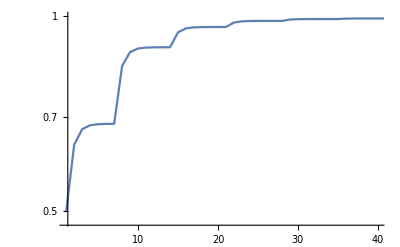

```mathematica
ListLogPlot[a,PlotRange->{{1,40},All},Joined->True]
```

```mathematica
Table[A a+B b+cc c+dd d,
{a,1,10},
{b,1,10},
{c,1,10},
{d,1,10}
][[2]]
```

{{{2 A+B+cc+dd,2 A+B+cc+2 dd,2 A+B+cc+3 dd,2 A+B+cc+4 dd,2 A+B+cc+5 dd,2 A+B+cc+6 dd,2 A+B+cc+7 dd,2 A+B+cc+8 dd,2 A+B+cc+9 dd,2 A+B+cc+10 dd},{2 A+B+2 cc+dd,2 A+B+2 cc+2 dd,2 A+B+2 cc+3 dd,2 A+B+2 cc+4 dd,2 A+B+2 cc+5 dd,2 A+B+2 cc+6 dd,2 A+B+2 cc+7 dd,2 A+B+2 cc+8 dd,2 A+B+2 cc+9 dd,2 A+B+2 cc+10 dd},6,{2 A+B+9 cc+dd,2 A+B+9 cc+2 dd,2 A+B+9 cc+3 dd,2 A+B+9 cc+4 dd,2 A+B+9 cc+5 dd,2 A+B+9 cc+6 dd,2 A+B+9 cc+7 dd,2 A+B+9 cc+8 dd,2 A+B+9 cc+9 dd,2 A+B+9 cc+10 dd},{2 A+B+10 cc+dd,2 A+B+10 cc+2 dd,2 A+B+10 cc+3 dd,2 A+B+10 cc+4 dd,2 A+B+10 cc+5 dd,2 A+B+10 cc+6 dd,2 A+B+10 cc+7 dd,2 A+B+10 cc+8 dd,2 A+B+10 cc+9 dd,2 A+B+10 cc+10 dd}},8,{{1},8,{1}}}
 |  |  |  |

## save

-Graphics-

```mathematica
1. Pn[0,nbar[ωtrCs[[1]],TCs]]Pn[0,nbar[ωtrNa[[1]],TNa]] Pn[0,nbar[ωtrCs[[2]],TCs]]Pn[0,nbar[ωtrNa[[2]],TNa]] Pn[0,nbar[ωtrCs[[3]],TCs]]Pn[0,nbar[ωtrNa[[3]],TNa]]
```

0.999253

## w/e

```mathematica
Δσ[TCs_,TNa_,τLoss_,ωtrNa_,ωtrCs_,maxNa_,maxCs_,ΔTCs_,ΔTNa_,ΔτLoss_,ΔωtrNa_,ΔωtrCs_]:=
Sqrt[
(D[σ[TCs0,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs], TCs0])^2 ΔTCs^2+
(D[σ[TCs,TNa0,τLoss,ωtrNa,ωtrCs,maxNa,maxCs], TNa0])^2 ΔTNa^2+
(D[σ[TCs,TNa,τLoss0,ωtrNa,ωtrCs,maxNa,maxCs], τLoss0])^2 ΔτLoss^2+
(D[σ[TCs,TNa,τLoss,ωtrNa0,ωtrCs,maxNa,maxCs], ωtrNa0])^2 ΔωtrNa^2+
(D[σ[TCs,TNa,τLoss,ωtrNa,ωtrCs0,maxNa,maxCs], ωtrCs0])^2 ΔωtrCs^2
]/.{TCs0->TCs,TNa0->TNa,τLoss0->τLoss,ωtrNa0->ωtrNa,ωtrCs0->ωtrCs}

Δσ[TCs,TNa,τLoss,ωtrNa,ωtrCs,maxNa,maxCs,ΔTCs,ΔTNa,ΔτLoss,ΔωtrNa,ΔωtrCs]/cm^2
```

2.68268×10^-14

1.15894×10^-14

# monte carlo+classical trajectory...

-sample some n, and therefore energy ϵn, from thermal distr
-this gives phase space trajectory, p=Pmax cos, x = Xmax sin
-take random phase.
-time evolve. 
-repeat for x,y,z dimensions
-at every time step, see if r<sigma. if it is, lose atom at that point. 

sigma=  pi r^2, so use sqrt(sigma/pi)

YOU NEED TO INCLUDE ANISOTROPY OF TRAP. because other wise you just get a 80kHz 3d ellipse which will either collide witin the first period or not... eed to get the lissajous figure....

DO I HAVE TO PROJECT sigma ONtO NROMAL TO VELOCITY VECTOR???
NO

DO I HAVE TO TAKE INTO ACCOUNT INSTANTANEOUS VELOCITY? ie if they are actually travelling away from each other....
NO I DON”T THINK SO

WTF... why doesn’t it work. can I redo this simulation with straight line propagation thru a uniform medium?

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
```

```mathematica
Clear[coordsInit]
coordsInit[T0_,m0_,fx0_,fy0_,fz0_,nSim0_]:=Module[{T=T0,m=m0,fx=fx0,fy=fy0,fz=fz0,nSim=nSim0},
Reap[
Do[(*loop nSim times*)
coordsInitSingle=Reap[
Do[(*loop over 3 axes*)
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
nCutoff=10 Ceiling[nbar];
Pn=Table[nbar^n/(nbar+1)^(n+1),{n,0,nCutoff}]; (*probability distribution*)
Cn=Accumulate[Pn]; (*cumulative distr*)

(*sample n from a probability distribution Pn*)
(*compare random number to cumulative distribution. put 1 if positive, 0 if negative.*)
listpn=Boole[Positive[#]]&/@(RandomReal[]-Cn);
(*the total of this list gives the corresponding n*)
n=Total[listpn];


ϵn=(n+1/2)ℏ 2π f;

xMax=(√ϵn)/(√(1/2 m)(2π f));
(*vMax=(√(2 m ϵn))/m; *)

(*randomly sample initial phase*)
θ=RandomReal[2π];
coordstemp={xMax,(*vMax,*)θ};

Sow[coordstemp],
{f,{fx,fy,fz}}
]
][[2,1]];

(*list of the form {{xMax,yMax,zMax},{vxMax,vyMax,vzMax},{θx,θy,θz}}*)
(*no v calculated...*)
coordsInitSingle=Transpose[coordsInitSingle];
Sow[coordsInitSingle]
,{j,nSim}]
][[2,1]]
];
(*list of nSim coordinates: {{xMax,yMax,zMax},{vxMax,vyMax,vzMax},{θx,θy,θz}}*)
(*no v calculated...*)
```

```mathematica
{fxNa,fyNa,fzNa}={500,500,80}{1+RandomVariate[NormalDistribution[0,.1]],1+RandomVariate[NormalDistribution[0,.1]],1+RandomVariate[NormalDistribution[0,.1]]}kHz;{491,513,82} kHz/4;
{fxCs,fyCs,fzCs}={145,145,25}{1+RandomVariate[NormalDistribution[0,.1]],1+RandomVariate[NormalDistribution[0,.1]],1+RandomVariate[NormalDistribution[0,.1]]}kHz;{147,143,25} kHz;
nSim=1;
coordsNa=coordsInit[70uK/4,mNa,fxNa,fyNa,fzNa,nSim];
coordsCs=coordsInit[10uK,mCs,fxCs,fyCs,fzCs,nSim];

k=1;
(*for the first realization*)
r[t_,fx_,fy_,fz_,θx_,θy_,θz_,X_,Y_,Z_]:=({X Cos[2π fx t+θx],Y Cos[2π fy t+θy],Z Cos[2π fz t+θz]});

{{X,Y,Z},{θx,θy,θz}}=coordsNa[[k]];
{x1,y1,z1}=r[t,fxNa,fyNa,fzNa,θx,θy,θz,X,Y,Z];

{{X,Y,Z},{θx,θy,θz}}=coordsCs[[k]];
{x2,y2,z2}=r[t,fxCs,fyCs,fzCs,θx,θy,θz,X,Y,Z];
```

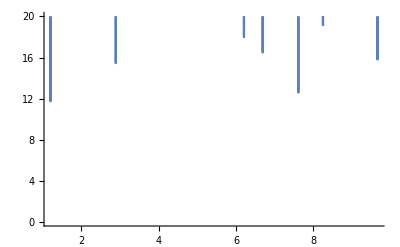

```mathematica
Plot[√(((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)/((1.4 10^-14 cm^2)/π)),{t,0,10},PlotRange->{All,{0,20}}]
```

## having 10x higher temperature does nt increase likelihood to meet?????